```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bwu/Documents/pp/v2/git/ppv2

## Glauber model

### Glauber model in optical limit (nucl-ex/0701025)

Woods - Saxon nuclear density distribution:

```mathematica
Rws=1.12*A^(1/3)-0.86 A^(-1/3)/.A-> 208 (*in fm*)
δws=0.54
ρws[x_,y_,z_]:=1/1223.740507900319 1/(ⅇ^((Sqrt[x^2+y^2+z^2]-6.490843321278989)/0.54)+1)
Tws[x_?NumericQ,y_?NumericQ]:=NIntegrate[ρws[x,y,z],{z,-∞,∞}]
(*Plot3D[Tws[x,y],{x,-10,10.},{y,-10,10}]*)
```

6.49084

0.54

```mathematica
Tls=Table[{b,Tws[b,0]},{b,0,20,0.1}];
```

```mathematica
TInterp=Interpolation[Tls]
```

InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
TwsInterp[b_]:=If[0.0<=b≤20.0,TInterp[b],0.0];
```

The Thickness function in 1/fm^2 :

```mathematica
TAB[bx_?NumericQ,by_?NumericQ]:=NIntegrate[ρws[sx,sy,zA]*ρws[sx-bx,sy-by,zB],{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},{zB,-Infinity,Infinity},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->10^4}}]
```

The total number of nucleon - nucleon collisions the inelastic cross section  of nucleon - nucleon collisions σi in mb=0.1 fm^2):

Let us naively compare to Table II with b = b mean and  σ_inel^NN=64 mb in arXiv : 1102.1957:

The inelastic cross section:
-Graphics-
σi in mb (=0.1 fm^2) while TAB in fm^-2.

```mathematica
dσABdb[b_,σi_]:=(1-(1-0.1*TAB[b,0]*σi)^(208*208))
```

Total inelastic nucleus - nucleus cross section in barn:
1 fm^2 = 0.01 barn.

```mathematica
σAB[σi_?NumericQ]:=0.02 π NIntegrate[ dσABdb[b,σi]b,{b,0,40},Method->"AdaptiveMonteCarlo"]
```

```mathematica
σNN=64.0
```

64.

```mathematica
σAB[64.0]
```

7.66576

```mathematica
σtot2p76=7.665761213905201
```

7.66576

```mathematica
(*1/σ dσ/db in fm^-1*)
dσdb[b_,σi_]:=1/σtot2p76 0.02*π*dσABdb[b,σi]b
```

```mathematica
NIntegrate[ρws[x,y,z],{x,-40,40},{y,-40,40},{z,-40,40}]
```

1.

```mathematica
Rrms =Sqrt[NIntegrate[ρws[x,y,z] (x^2+y^2+z^2),{x,-40,40},{y,-40,40},{z,-40,40}]]
```

5.41367

```mathematica
0.01*4π Rrms^2
```

3.68293

```mathematica
dσdbls=Table[{b,dσdb[b,σNN]},{b,0,20,0.1}]
```

{{0.,0.},{0.1,0.000819643},{0.2,0.00163929},{0.3,0.00245893},{0.4,0.00327857},{0.5,0.00409821},{0.6,0.00491786},{0.7,0.0057375},{0.8,0.00655714},{0.9,0.00737678},{1.,0.00819643},{1.1,0.00901607},{1.2,0.00983571},{1.3,0.0106554},{1.4,0.011475},{1.5,0.0122946},{1.6,0.0131143},{1.7,0.0139339},{1.8,0.0147536},{1.9,0.0155732},{2.,0.0163929},{2.1,0.0172125},{2.2,0.0180321},{2.3,0.0188518},{2.4,0.0196714},{2.5,0.0204911},{2.6,0.0213107},{2.7,0.0221304},{2.8,0.02295},{2.9,0.0237696},{3.,0.0245893},{3.1,0.0254089},{3.2,0.0262286},{3.3,0.0270482},{3.4,0.0278679},{3.5,0.0286875},{3.6,0.0295071},{3.7,0.0303268},{3.8,0.0311464},{3.9,0.0319661},{4.,0.0327857},{4.1,0.0336054},{4.2,0.034425},{4.3,0.0352446},{4.4,0.0360643},{4.5,0.0368839},{4.6,0.0377036},{4.7,0.0385232},{4.8,0.0393429},{4.9,0.0401625},{5.,0.0409821},{5.1,0.0418018},{5.2,0.0426214},{5.3,0.0434411},{5.4,0.0442607},{5.5,0.0450803},{5.6,0.0459},{5.7,0.0467196},{5.8,0.0475393},{5.9,0.0483589},{6.,0.0491786},{6.1,0.0499982},{6.2,0.0508178},{6.3,0.0516375},{6.4,0.0524571},{6.5,0.0532768},{6.6,0.0540964},{6.7,0.0549161},{6.8,0.0557357},{6.9,0.0565553},{7.,0.057375},{7.1,0.0581946},{7.2,0.0590143},{7.3,0.0598339},{7.4,0.0606536},{7.5,0.0614732},{7.6,0.0622928},{7.7,0.0631125},{7.8,0.0639321},{7.9,0.0647518},{8.,0.0655714},{8.1,0.0663911},{8.2,0.0672107},{8.3,0.0680303},{8.4,0.06885},{8.5,0.0696696},{8.6,0.0704893},{8.7,0.0713089},{8.8,0.0721286},{8.9,0.0729482},{9.,0.0737678},{9.1,0.0745875},{9.2,0.0754071},{9.3,0.0762268},{9.4,0.0770464},{9.5,0.0778661},{9.6,0.0786857},{9.7,0.0795053},{9.8,0.080325},{9.9,0.0811446},{10.,0.0819643},{10.1,0.0827839},{10.2,0.0836036},{10.3,0.0844232},{10.4,0.0852428},{10.5,0.0860625},{10.6,0.0868821},{10.7,0.0877018},{10.8,0.0885214},{10.9,0.0893411},{11.,0.0901607},{11.1,0.0909803},{11.2,0.0918},{11.3,0.0926196},{11.4,0.0934393},{11.5,0.0942589},{11.6,0.0950786},{11.7,0.0958982},{11.8,0.0967178},{11.9,0.0975375},{12.,0.0983571},{12.1,0.0991768},{12.2,0.0999964},{12.3,0.100816},{12.4,0.101636},{12.5,0.102455},{12.6,0.103275},{12.7,0.104095},{12.8,0.104914},{12.9,0.105734},{13.,0.106554},{13.1,0.107373},{13.2,0.108193},{13.3,0.109012},{13.4,0.109829},{13.5,0.11064},{13.6,0.111441},{13.7,0.112203},{13.8,0.112909},{13.9,0.113514},{14.,0.113896},{14.1,0.114102},{14.2,0.113606},{14.3,0.113151},{14.4,0.111601},{14.5,0.109521},{14.6,0.106486},{14.7,0.102549},{14.8,0.0986497},{14.9,0.0927443},{15.,0.0880934},{15.1,0.0816317},{15.2,0.0762187},{15.3,0.0700711},{15.4,0.0627115},{15.5,0.0578589},{15.6,0.0521466},{15.7,0.046082},{15.8,0.0415663},{15.9,0.0367689},{16.,0.0324755},{16.1,0.0291749},{16.2,0.024985},{16.3,0.0222866},{16.4,0.019181},{16.5,0.0169933},{16.6,0.0143245},{16.7,0.012714},{16.8,0.0109771},{16.9,0.00966226},{17.,0.00839944},{17.1,0.00714416},{17.2,0.00612242},{17.3,0.00520124},{17.4,0.00453378},{17.5,0.00392697},{17.6,0.00335644},{17.7,0.00284944},{17.8,0.00247769},{17.9,0.00211377},{18.,0.00180184},{18.1,0.00158239},{18.2,0.00131762},{18.3,0.00114304},{18.4,0.000975525},{18.5,0.000830237},{18.6,0.000713205},{18.7,0.000616971},{18.8,0.000520802},{18.9,0.000453937},{19.,0.00038277},{19.1,0.000325913},{19.2,0.000274657},{19.3,0.000237576},{19.4,0.000201246},{19.5,0.00017295},{19.6,0.000145139},{19.7,0.00012437},{19.8,0.000105561},{19.9,0.000089904},{20.,0.0000760572}}

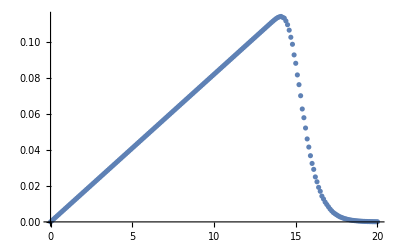

```mathematica
ListPlot[dσdbls]
```

Check normalization :

```mathematica
0.1*(Total[dσdbls[[2;;-2,2]]]+1/2(dσdbls[[1,2]]+dσdbls[[-1,2]]))
```

0.991478

So it does not do the trick.

```mathematica
dσdbInterp=Interpolation[dσdbls,InterpolationOrder->1]
```

InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
NIntegrate[dσdbInterp[b],{b,0,20}]
```

1.01053

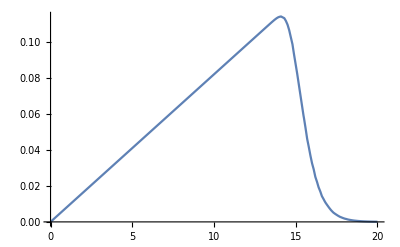

```mathematica
Plot[dσdbInterp[b],{b,0,20}]
```

To compare with pi - pi :

```mathematica
Transpose[{(dσdbls[[1;;-1,1]]/Rrms),Rrms dσdbls[[1;;-1,2]]}]
```

{{0.,0.},{0.0184718,0.00443727},{0.0369435,0.00887455},{0.0554153,0.0133118},{0.0738871,0.0177491},{0.0923588,0.0221864},{0.110831,0.0266236},{0.129302,0.0310609},{0.147774,0.0354982},{0.166246,0.0399355},{0.184718,0.0443727},{0.203189,0.04881},{0.221661,0.0532473},{0.240133,0.0576845},{0.258605,0.0621218},{0.277076,0.0665591},{0.295548,0.0709964},{0.31402,0.0754336},{0.332492,0.0798709},{0.350964,0.0843082},{0.369435,0.0887455},{0.387907,0.0931827},{0.406379,0.09762},{0.424851,0.102057},{0.443322,0.106495},{0.461794,0.110932},{0.480266,0.115369},{0.498738,0.119806},{0.517209,0.124244},{0.535681,0.128681},{0.554153,0.133118},{0.572625,0.137555},{0.591097,0.141993},{0.609568,0.14643},{0.62804,0.150867},{0.646512,0.155305},{0.664984,0.159742},{0.683455,0.164179},{0.701927,0.168616},{0.720399,0.173054},{0.738871,0.177491},{0.757342,0.181928},{0.775814,0.186365},{0.794286,0.190803},{0.812758,0.19524},{0.831229,0.199677},{0.849701,0.204115},{0.868173,0.208552},{0.886645,0.212989},{0.905117,0.217426},{0.923588,0.221864},{0.94206,0.226301},{0.960532,0.230738},{0.979004,0.235175},{0.997475,0.239613},{1.01595,0.24405},{1.03442,0.248487},{1.05289,0.252925},{1.07136,0.257362},{1.08983,0.261799},{1.10831,0.266236},{1.12678,0.270674},{1.14525,0.275111},{1.16372,0.279548},{1.18219,0.283985},{1.20066,0.288423},{1.21914,0.29286},{1.23761,0.297297},{1.25608,0.301735},{1.27455,0.306172},{1.29302,0.310609},{1.3115,0.315046},{1.32997,0.319484},{1.34844,0.323921},{1.36691,0.328358},{1.38538,0.332795},{1.40385,0.337233},{1.42233,0.34167},{1.4408,0.346107},{1.45927,0.350545},{1.47774,0.354982},{1.49621,0.359419},{1.51468,0.363856},{1.53316,0.368294},{1.55163,0.372731},{1.5701,0.377168},{1.58857,0.381605},{1.60704,0.386043},{1.62552,0.39048},{1.64399,0.394917},{1.66246,0.399355},{1.68093,0.403792},{1.6994,0.408229},{1.71787,0.412666},{1.73635,0.417104},{1.75482,0.421541},{1.77329,0.425978},{1.79176,0.430415},{1.81023,0.434853},{1.8287,0.43929},{1.84718,0.443727},{1.86565,0.448165},{1.88412,0.452602},{1.90259,0.457039},{1.92106,0.461476},{1.93954,0.465914},{1.95801,0.470351},{1.97648,0.474788},{1.99495,0.479225},{2.01342,0.483663},{2.03189,0.4881},{2.05037,0.492537},{2.06884,0.496975},{2.08731,0.501412},{2.10578,0.505849},{2.12425,0.510286},{2.14272,0.514724},{2.1612,0.519161},{2.17967,0.523598},{2.19814,0.528035},{2.21661,0.532473},{2.23508,0.53691},{2.25356,0.541347},{2.27203,0.545785},{2.2905,0.550222},{2.30897,0.554659},{2.32744,0.559096},{2.34591,0.563534},{2.36439,0.567971},{2.38286,0.572408},{2.40133,0.576845},{2.4198,0.581283},{2.43827,0.585719},{2.45674,0.590152},{2.47522,0.594576},{2.49369,0.598971},{2.51216,0.603304},{2.53063,0.607431},{2.5491,0.611251},{2.56758,0.614524},{2.58605,0.616594},{2.60452,0.617712},{2.62299,0.615025},{2.64146,0.612561},{2.65993,0.604171},{2.67841,0.59291},{2.69688,0.576478},{2.71535,0.555169},{2.73382,0.534057},{2.75229,0.502087},{2.77076,0.476908},{2.78924,0.441927},{2.80771,0.412623},{2.82618,0.379342},{2.84465,0.339499},{2.86312,0.313229},{2.8816,0.282304},{2.90007,0.249473},{2.91854,0.225026},{2.93701,0.199054},{2.95548,0.175812},{2.97395,0.157943},{2.99243,0.13526},{3.0109,0.120652},{3.02937,0.10384},{3.04784,0.0919959},{3.06631,0.077548},{3.08478,0.0688295},{3.10326,0.0594265},{3.12173,0.0523083},{3.1402,0.0454718},{3.15867,0.0386761},{3.17714,0.0331448},{3.19562,0.0281578},{3.21409,0.0245444},{3.23256,0.0212593},{3.25103,0.0181707},{3.2695,0.0154259},{3.28797,0.0134134},{3.30645,0.0114433},{3.32492,0.00975458},{3.34339,0.00856655},{3.36186,0.00713317},{3.38033,0.00618804},{3.39881,0.00528117},{3.41728,0.00449463},{3.43575,0.00386105},{3.45422,0.00334007},{3.47269,0.00281945},{3.49116,0.00245746},{3.50964,0.00207219},{3.52811,0.00176438},{3.54658,0.0014869},{3.56505,0.00128616},{3.58352,0.00108948},{3.60199,0.000936294},{3.62047,0.000785735},{3.63894,0.000673298},{3.65741,0.00057147},{3.67588,0.00048671},{3.69435,0.000411748}}

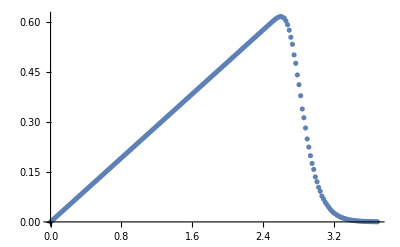

```mathematica
ListPlot[%]
```